```mathematica
gravConst=6.67428*10^(-11);
me=6.0*10^24;
re=6.357*10^6;
dt=1.0;

Clear[Simulator];
Simulator[{x0_,v0_},te_Integer,controlFunc_]:=
Module[{iterFunc},
iterFunc[{st_,vt_}]:=With[{gt=-gravConst*me/Norm[st]^2*st/Norm[st],
dv=controlFunc[st]},
Block[{stt=st+(vt*dt)+1/2*(gt+dv)*dt^2,gtt},
gtt=-gravConst*me/Norm[stt]^2*stt/Norm[stt];
{stt,vt+(dv+(gt+gtt)/2)*dt
}]];
NestList[iterFunc,{x0,v0},te]
]
```

```mathematica
res=Simulator[{{0,-(100000+re)},{7875.214,0}},20000,{0,0}&];
```

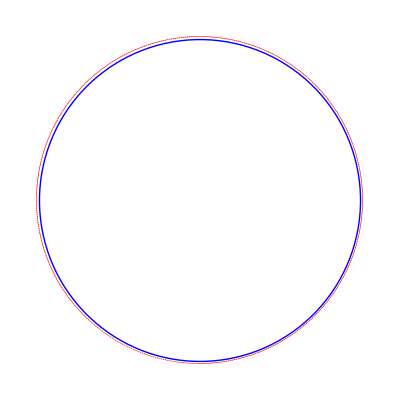

```mathematica
Graphics[{Blue,Circle[{0,0},re],Red,PointSize[0.001],Point[res[[1;;-1;;10,1]]]}]
```

```mathematica
re+r2/.rule
```

1.3714×10^7

```mathematica
res[[1;;-1;;1000,1]]
```

{{0,-6.457×10^6},{6.32495×10^6,-2.29431×10^6},{5.33975×10^6,4.8172×10^6},{-1.06772×10^6,7.27364×10^6}}

```mathematica
Subtract@@(Norm/@res[[{1,-1},1]])
```

-0.0133284